## Preamble

```mathematica
LaunchKernels[10];
<< KerrGeodesics`
<< GeneralRelativityTensors`
<<SpinWeightedSpheroidalHarmonics`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"];
ParallelNeeds["Teukolsky`"];
ParallelNeeds["KerrGeodesics`"];
Information[PacletObject["Teukolsky"]]
```

Paclet

## Calculating ϕ_1

## Calculating homogenous Φ_1 given a radius r

```mathematica
ϕ1[a_,p_,e_, l_,m_,n_]:=Module[{Ω,ω, Σ, Δ, Trad, Tradmino, orbit, t0,r0,θ0, ϕ0, Q0,K0,Β, λ, prec=32},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,1];
ω=m Ω[[3]] + n Ω[[1]];
Trad =2π/Ω[[1]];
Tradmino=2π/KerrGeoFrequencies[a,p,e,1,Time->"Mino"][[1]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],SetPrecision[1,prec]];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
Q0 := m-a ω[m,n];
K0[λ_]:= ω[m,n](r0[λ]^2 + a^2)- a m;
λ = SpinWeightedSpheroidalEigenvalue[1,l,m,a ω];
Β= Sqrt[λ^2+ 4 a m ω - 4 a^2 ω^2];
(*To Do: calculate g_(+1) and Subscript[f, -1] and then combine them to calculate Subscript[ϕ, 1]*)
]
```

## Calculating ϕ_0 and ϕ_2

```mathematica
OrbitTP[p_,e_]:= Module[{},{rMax, rMin}/.NSolve[{p== (2 rMax rMin)/(rMax + rMin), e == (rMax-rMin)/(rMax + rMin)}, {rMax, rMin}][[1]]
]
```

```mathematica
LMAX = 5;NMAX=2;
```

```mathematica
Φ0 [a_ , r_ ,τmino_, p_,e_,l_]:= Module[{Δ,Ω,orbit, rmin, rmax,sum,t0,r0,θ0,ϕ0, M=1,prec= 32},
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,1,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,1,NMAX}
];
];
 Δ^-1 Total[Flatten[sum]]
]
```

```mathematica
Φ2 [a_ , r_ ,τmino_, p_,e_,l_]:= Module[{Δ,Ω,orbit, rmin, rmax,sum,t0,r0,θ0,ϕ0, M=1,prec= 32},
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,1,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,1,NMAX}
];
];
1/(2(r-ⅈ a Cos[θ0[τmino]])^2)Δ^-1 Total[Flatten[sum]]
]
```

## Plotting Φ_0

### Sum over l

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
lowerΦ0 = Monitor[Table[Φ0 [a , lowerRs[[i]] ,τmino, p,e,1],{i,1 ,Length[lowerRs]}],i];
upperΦ0 =Monitor[Table[Φ0 [a , upperRs[[i]] ,τmino, p,e,1],{i,1 ,Length[lowerRs]}],50+i];
]
```

$Aborted

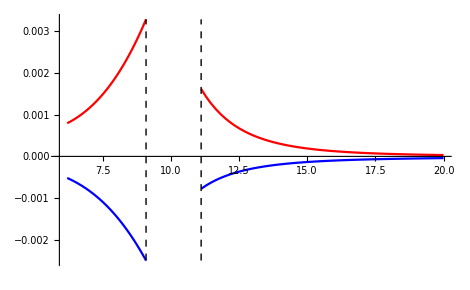

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[lowerΦ0],Im[lowerΦ0], Re[upperΦ0],Im[upperΦ0]}];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ0[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ0[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
]
```

### l = 1 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ0s= Monitor[ParallelTable[Φ0 [a , Rs[[i]] ,τmino, p,e,1],{i,1 ,Length[Rs]}],i];
]
```

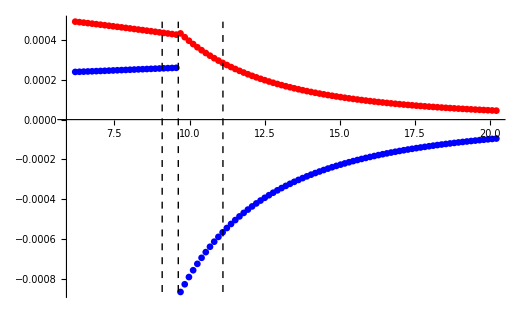

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

### l=2 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ0s= Monitor[ParallelTable[Φ0 [a , Rs[[i]] ,τmino, p,e,2],{i,1 ,Length[Rs]}],i];
]
```

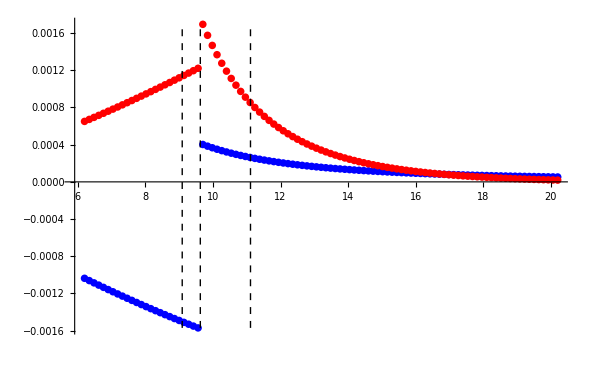

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

## Plotting Φ_2

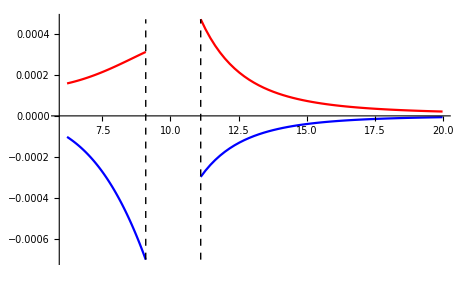

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
lowerΦ2 = Monitor[Table[Φ2 [a , lowerRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}],i];
upperΦ2 =Monitor[Table[Φ2 [a , upperRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}],50+i];
]
Module[{rmax, rmin, AllData, lineStyle, line1, line2},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[lowerΦ2],Im[lowerΦ2], Re[upperΦ2],Im[upperΦ2]}];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ2[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ2[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ2[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ2[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
]
```

Haas(2012) and  Thesis by Patrick Nolan (UCD)

### l = 1 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ2s= Monitor[ParallelTable[Φ2 [a , Rs[[i]] ,τmino, p,e,1],{i,1 ,Length[Rs]}],i];
]
```

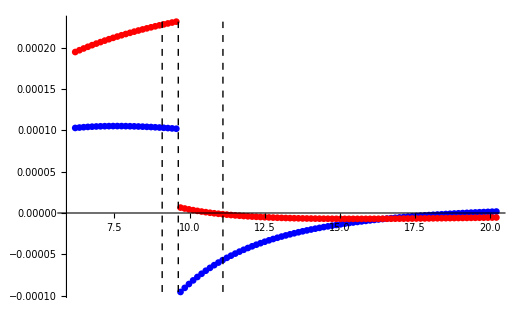

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ2s],Im[Φ2s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

### l=2 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ2s= Monitor[ParallelTable[Φ2[a , Rs[[i]] ,τmino, p,e,2],{i,1 ,Length[Rs]}],i];
]
```

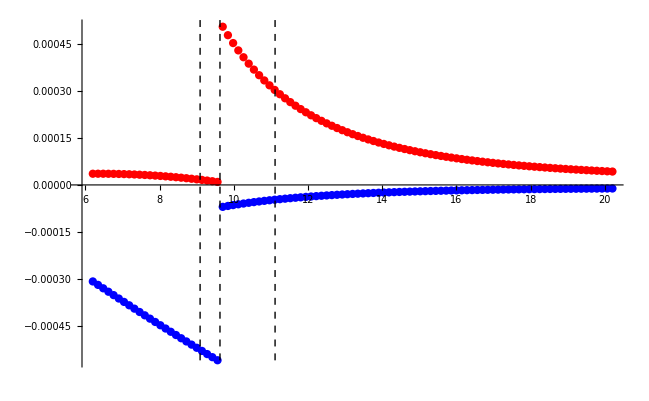

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}, PlotRange->All
]
]
```